Here is a useful (but old) reference thesis
https://repository.rice.edu/server/api/core/bitstreams/1efb2ace-0a37-422e-be4d-0f3d4616f6d4/content
Accelerating the Arnoldi Iteration: theory and practice
Chao Yang Doctoral Thesis 
Rice University 1998
D Sorensen Advisor

# Arnoldi and AD

I want to differentiate the “incremental” version of the Arnoldi code.  The plan is to add one “direction” to the “positive subdiagonal code” code first.  Then revaluate.

### Original code and cleaned test

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

```mathematica
m=300;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
ListPlot[ReIm[Eigenvalues[A]],PlotStyle->Large];
n=10;
{Q,H}={{Normalize[RandomReal[{-1,1},m]]}ᵀ,{{}}};
Do[
{Q,H}=Arnoldi[A][{Q,H}],
{n}]
TableForm[{
{UpperTriangularMatrixQ[H,-1],OrthogonalMatrixQ[Q]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}],
{Min[Diagonal[H,-1]],H⟦n+1,n⟧}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},None}]
```

Structure | True | True
Dimensions | True | True
Residuals | 5.12555×10^-16 | 6.84252×10^-16
Subdiagonal | 0.746241 | 0.788955

### First Pass AD Code and test

I want to differentiate Arnoldi with respect to the initialization b by adding an orthogonal perturbation b→b+ϵ_1 db_1 I need to add a dQ and dH to the updater.

```mathematica
ArnoldiAD1[A_][{{Q_,H_},{dQ_,dH_}}]:= Module[{m,n,HNew,dHNew,w,dw,q,dq,γ,dγ},
{m,n}=Dimensions[Q];
(* Duplicating the Initialization for HNew *)
dHNew=ConstantArray[0,{n+1,n}];dHNew⟦1;;n,1;;n-1⟧=dH;
HNew  =ConstantArray[0,{n+1,n}];  HNew⟦1;;n,1;;n-1⟧=H;
(* Duplicating the computation for w for dw *)
dw = A.dQ⟦All,n⟧;
w   =A.Q⟦All,n⟧;
Do[
(* duplicate for dq *)
dq=dQ⟦All,k⟧;
q=Q⟦All,k⟧;
(* product rule for dHNew *)
dHNew⟦k,n⟧=dq.w+q.dw;
HNew⟦k,n⟧=q.w;
(* product rule for dw update *)
dw=dw-dHNew⟦k,n⟧ q- HNew⟦k,n⟧ dq;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
(* Chain rule for γ=√(w.w) *)
γ=Norm[w];
dγ=(w.dw)/γ;
dHNew⟦n+1,n⟧=dγ;
HNew⟦n+1,n⟧=γ;
(* product/quotient rule for w = w/γ = w γ^-1 *)
dw =dw γ^-1 - w γ^-2 dγ;
w=w/HNew⟦n+1,n⟧;
(* Repackage the output *) 
{{ArrayFlatten[({{Q, {w}ᵀ}})],HNew},
{ArrayFlatten[({{dQ, {dw}ᵀ}})],dHNew}}
]
```

```mathematica
m=22;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
n=6;
(* Initialize {Q, H}  *)
b=Normalize[RandomReal[{-1,1},m]];
{Q,H}={{b}ᵀ,{{}}};
(* Initialize {dQ, dH}  *)
(* Make sure b1 is perp to b and unit length *)
b1=RandomReal[{-1,1},m];
b1=Normalize[b1-(b1.b)b];
{dQ,dH}={{b1}ᵀ,{{}}};
Do[
(*{Q,H}=Arnoldi[A][{Q,H}]; *)
{{Q,H},{dQ,dH}}=ArnoldiAD1[A][{{Q,H},{dQ,dH}}],
{n}]
TableForm[{
{OrthogonalMatrixQ[Q],UpperTriangularMatrixQ[H,-1]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n},Dimensions[dQ]=={m,n+1},Dimensions[dH]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H,Qᵀ.dQ +dQᵀ.Q, A.dQ⟦All,1;;n⟧-dQ.H-Q.dH}],
{" ",Min[Diagonal[H,-1]], " ", Min[Diagonal[dH,-1]]}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},{"Q","H","dQ","dH"}}]
```

| Q | H | dQ | dH
Structure | True | True |  | 
Dimensions | True | True | True | True
Residuals | 4.80931×10^-16 | 2.82693×10^-16 | 7.55893×10^-16 | 2.72564×10^-16
Subdiagonal |   | 0.553142 |   | -0.271006

The plan is to work out how big  a perturbation might need to be to make H_(n+1,n)==0.

```mathematica
Solve[H⟦n+1,n⟧ + ϵ dH⟦n+1,n⟧==0,ϵ]
LinearSolve[ {{dH⟦n+1,n⟧}},{-H⟦n+1,n⟧}]
```

{{ϵ→-1.65751}}

{-1.65751}

### Second Pass AD Code and test. XXX

I want to compute  multiple derivatives at the same time. 
	b⃗+G.ϵ⃗
where I might as well assume that G∈ℝ^(m×s) is orthogonal and Gᵀ.b=0_s

I am testing on the single direction code on several separate directions first.

```mathematica
m=812;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
n=12;
(* Initialize initialize base direction b and perturbation directions G  *)
s=36;
bG=QRDecomposition[RandomReal[{-1,1},{m,s+1}]]⟦1⟧ᵀ;
b=bG⟦All,1⟧;
G=bG⟦All,2;;-1⟧;
(* Initialize {Q, H}  *)
TableForm[Table[
{Q,H}={{b}ᵀ,{{}}};
(* Initialize {dQ, dH}  *)
{dQ[i],dH[i]}={G⟦All,{i}⟧,{{}}};
Do[
{{Q,H},{dQ[i],dH[i]}}=ArnoldiAD1[A][{{Q,H},{dQ[i],dH[i]}}],
{n}];
TableForm[{
{OrthogonalMatrixQ[Q],UpperTriangularMatrixQ[H,-1]},
{Dimensions[Q]=={m,n+1},Dimensions[H]=={n+1,n},Dimensions[dQ[i]]=={m,n+1},Dimensions[dH[i]]=={n+1,n}},
Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H,
Qᵀ.dQ[i] +dQ[i]ᵀ.Q, A.dQ[i]⟦All,1;;n⟧-dQ[i].H-Q.dH[i]}],
{" ",Min[Diagonal[H,-1]], " ", Min[Diagonal[dH[i],-1]]}
},TableHeadings->{{"Structure","Dimensions","Residuals","Subdiagonal"},{"Q","H","dQ","dH"}}],
{i,1,s}]];
Mat={Table[dH[i]⟦n+1,n⟧,{i,1,s}]};
sol=LinearSolve[ Mat,{-H⟦n+1,n⟧}]
√(sol.sol);
(*vars=Array[ϵ,s];
FindMinimum[ {√(vars.vars),Mat.vars+H⟦n+1,n⟧==0.0},vars]*)
```

{0.772413,-0.798437,-0.237227,0.49084,0.772425,-0.605488,-0.900553,-0.759558,-0.708569,-0.606578,-1.7895,1.60534,0.600673,0.0660137,1.27735,0.00851818,-0.405949,0.703568,1.90942,0.326969,-0.33882,1.38573,1.22743,-0.907085,1.28547,-0.374195,-0.197793,0.074094,0.464844,0.0990194,0.542838,-0.362002,-0.353753,-1.00038,0.72614,0.700347}

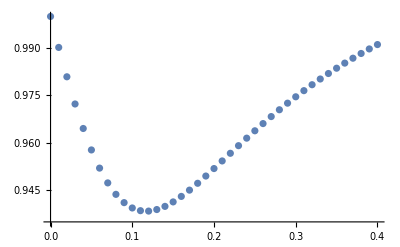

```mathematica
ListPlot[
Table[
bNew=Normalize[b+ϵ G.sol];
{QNew,HNew}={{bNew}ᵀ,{{}}};
Do[
{QNew,HNew}=Arnoldi[A][{QNew,HNew}],
{n+1}];
{ϵ,HNew⟦n+1,n⟧/H⟦n+1,n⟧},
{ϵ,0.0,0.4,0.01}],
PlotRange->All
]
```

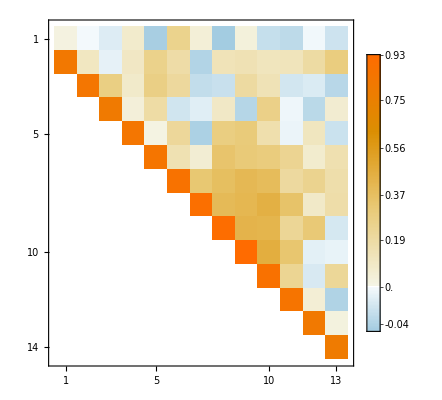

```mathematica
MatrixPlot[HNew,PlotLegends->Automatic]
```

```mathematica
Table[
]
```